# Using Functions to create Curves, Surfaces, and Shapes in 3D

Math 250 - Mathematical Computing
Christopher Hanusa

## 11.1 Overview

In this tutorial, we explore how to create curves, surfaces, and shapes in three dimensions, with an eye toward making them 3D printable.

## 11.2 Curves (1D)

To generate and 3D print curves in space, you will need to view them as vector-valued functions f:ℝ^1→ℝ^3.  (Wikipedia Link: https://en.wikipedia.org/wiki/Vector-valued_function)  In other words, you can think of them as functions of time, where as time changes, the tip of the vector sweeps out a curve in (x,y,z)-space.  We are going to use ParametricPlot3D to create a visualization of the curve.

```mathematica
?ParametricPlot3D
```

Here is a function whose x-coordinate, y-coordinate, and z-coordinate change over time:
x(t)=sin(t)
y(t)=sin(2t)
z(t)=sin(3t)

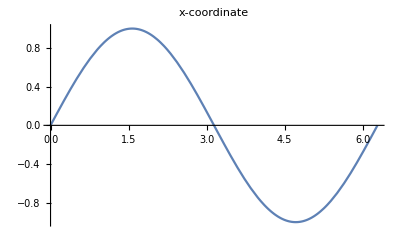
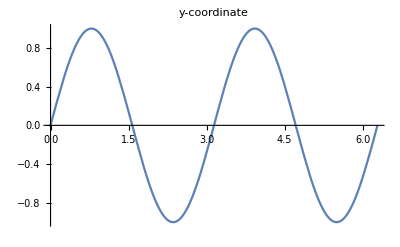
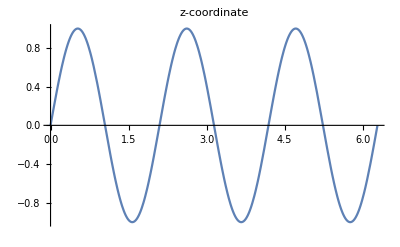

```mathematica
{Plot[Sin[t],{t,0,2Pi},PlotLabel->"x-coordinate"],
Plot[Sin[2t],{t,0,2Pi},PlotLabel->"y-coordinate"],
Plot[Sin[3t],{t,0,2Pi},PlotLabel->"z-coordinate"]}
```

When we put them all together, we get this very interesting curve:

```mathematica
ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotRange->All]
```

-Graphics3D-

To get a three-dimensional version of this curve, use the option PlotStyle->Tube[].

```mathematica
ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->Tube[.2],PlotRange->All]
```

-Graphics3D-

To add some color, add it to the PlotStyle options.

```mathematica
ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->{Orange,Tube[.1]},PlotRange->All]
```

-Graphics3D-

## 11.3 Graphs of functions of two variables (2D)

Plot3D is used to plot the graph of a two-dimensional function z=f(x,y).  Increase the number of PlotPoints to make the surface smoother.

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->None,PlotPoints->30]
```

-Graphics3D-

There is a secret option called Extrusion that allows you to thicken surfaces in order to be able to 3D print them.

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->None,PlotPoints->50,Extrusion->.2]
```

-Graphics3D-

You may also be interested in the related command ContourPlot3D

```mathematica
Row@{
ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,Boxed->False,Axes->False,ImageSize->200],
ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,Boxed->False,Axes->False,ImageSize->200,Extrusion->.1]
}
```

-Graphics3D--Graphics3D-

## 11.4 Parametrized surfaces (2D)

ParametricPlot3D also can be used to create parametrized surfaces when you have a function f:ℝ^2→ℝ^3.

Example 11.4.1. The points on a torus satisfy that the distance (r) of every point on the torus to the circle running through the torus (of radius R) is constant.  Mathematically, that is the equation:
(x - R cos (u))^2 + (y - R sin (u))^2 + z^2 = r^2.

This surface can be parametrized using the equations:
x(u,v)= R Cos[u] + r Cos[u] Cos[v],
y(u,v)= R  Sin[u] + r  Sin[u] Cos[v],
z(u,v)=                                      r  Sin[v]
Note that with two independent variables (u and v), the object swept out is a surface.  Compare this to when there is one independent variable (t) sweeping out the curve above.

Here is the torus whose outer radius is 3 and inner radius is 1.

```mathematica
torus=ParametricPlot3D[{(3+Cos[v]) Cos[u],(3+Cos[v]) Sin[u],Sin[v]},{u,0,2Pi},{v,0,2Pi},PlotStyle->Darker[Blend[{Orange,Yellow},.2]],Mesh->None,Boxed->False,Axes->False]
```

-Graphics3D-

Looks delicious!

Here is a link to more details about parametrizing surfaces

## 11.5 RegionPlot3D (3D)

Another way to plot a closed region in 3D space is to use RegionPlot3D.  It gives all the points in the specified region that satisfy your given requirements.

RegionPlot3D is especially useful for finding the intersection of two objects.

Example 11.5.1. What is the region inside two spheres?

```mathematica
spheres=Graphics3D[{Opacity[.3],Red,Sphere[{0,0,0},1],Blue,Sphere[{1,0,0},1]}]
```

-Graphics3D-

```mathematica
intersection=RegionPlot3D[
(x^2+y^2+z^2≤1)&&((x-1)^2+y^2+z^2≤1),
{x,-1,2},{y,-1.5,1.5},{z,-1.5,1.5},PlotPoints->100,MeshStyle->None]
```

-Graphics3D-

```mathematica
Show[spheres,intersection]
```

-Graphics3D-

We can also use Mathematica to create objects that have a solid base and an interesting surface as its top face.  When the bounding function is z=f(x,y), we can use RegionPlot3D to take the set of points that lie below the curve, which are of the form z<f(x,y).  Here are two examples: a parabolic bowl and a nice bumpy surface.  Notice that you need to think about which x, y, and z bounds will make your block look the best.  In both examples I am using the option BoxRatios→Automatic so that the axes are scaled so that the unit distance in each direction is the same.

```mathematica
bowlblock=RegionPlot3D[x^2+y^2>z>-(x^2+y^2),{x,-1,1},{y,-1,1},{z,-3,3},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
block=RegionPlot3D[Sin[x]+Sin[y]>z,{x,0-Pi/2,6Pi-Pi/2},{y,0-Pi/2,6Pi-Pi/2},{z,-3,3},PlotPoints->30,BoxRatios->Automatic]
```

-Graphics3D-

## 11.6 BSplineSurface (2D)

If you’d like to create a smooth surface from a set of control points (x_i,y_i,z_i), use BSplineSurface

```mathematica
cpts=Table[{i,j,RandomReal[{-1,1}]},{i,5},{j,5}];
```

```mathematica
b=Graphics3D[BSplineSurface[cpts]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,cpts],Gray,Line[cpts],Line[Transpose[cpts]]}],b]
```

-Graphics3D-

### Designing a Car

This is from the Wolfram Demonstration: “Designing a Car Body with Splines” available here:
http://demonstrations.wolfram.com/DesigningACarBodyWithSplines/

```mathematica
Manipulate[
Graphics3D[{
color,Specularity[White,50],
BSplineSurface[carbody,SplineDegree->Floor[degrees]],
If[mesh,
{Dashed,Blue,Line[carbody],Line[Transpose[carbody]],Red,PointSize[Medium],Point/@carbody},{}]},
Boxed->False,Lighting->"Neutral",RotationAction->"Clip",ViewPoint->{-2,-2,2}],
Row[{Control[{{degrees,{1,1}},{1,1},{14,7},ImageSize->{140,70}}],Dynamic[Floor[degrees]]},Spacer[10]],
Row[{Control[{color,ColorData["HTML","GoldenRod"]}],Control[{mesh,{False,True}}]},Spacer[10]],
Initialization:>(carbody={
{{-.2,-2.25,0},{-.2,-2.25,0},{-.2,-2,0},{-.2,0,0},{-.2,2,0},{-.2,2.25,0},{-.2,2.25,0}},
{{0,-2.25,0},{0,-2.25,1.75},{0,-2,1.75},{0,0,1.75},{0,2,1.75},{0,2.25,1.75},{0,2.25,0}},
{{1,-2.25,0},{1,-2.25,1.75},{1,-2,1.75},{1,0,1.75},{1,2,1.75},{1,2.25,1.75},{1,2.25,0}},
{{1.01,-2.25,1.5},{1.01,-2.25,1.75},{1.01,-2,1.75},{1.01,0,1.75},{1.01,2,1.75},{1.01,2.25,1.75},{1.01,2.25,1.5}},
{{2.99,-2.25,1.5},{2.99,-2.25,1.75},{2.99,-2,1.75},{2.99,0,1.75},{2.99,2,1.75},{2.99,2.25,1.75},{2.99,2.25,1.5}},
{{3,-2.25,0},{3,-2.25,1.75},{3,-2,1.75},{3,0,1.75},{3,2,1.75},{3,2.25,1.75},{3,2.25,0}},
{{4,-2.25,0},{4,-2.25,1.75},{4,-2,1.75},{4,0,1.75},{4,2,1.75},{4,2.25,1.75},{4,2.25,0}},
{{5,-2.25,0},{5,-2.25,1.75},{5,-2,3.5},{5,0,3.5},{5,2,3.5},{5,2.25,1.75},{5,2.25,0}},
{{8,-2.25,0},{8,-2.25,1.75},{8,-2,3.5},{8,0,3.5},{8,2,3.5},{8,2.25,1.75},{8,2.25,0}},
{{8.01,-2.25,1.5},{8.01,-2.25,1.75},{8.01,-2,3.5},{8.01,0,3.5},{8.01,2,3.5},{8.01,2.25,1.75},{8.01,2.25,1.5}},
{{9,-2.25,1.5},{9,-2.25,2},{9,-2,2},{9,0,2},{9,2,2},{9,2.25,2},{9,2.25,1.5}},
{{9.99,-2.25,1.5},{9.99,-2.25,2},{9.99,-2,2},{9.99,0,2},{9.99,2,2},{9.99,2.25,2},{9.99,2.25,1.5}},
{{10,-2.25,0},{10,-2.25,2},{10,-2,2},{10,0,2},{10,2,2},{10,2.25,2},{10,2.25,0}},
{{11,-2.25,0},{11,-2.25,2},{11,-2,2},{11,0,2},{11,2,2},{11,2.25,2},{11,2.25,0}},
{{11.01,-2.25,0},{11.01,-2.25,0},{11.01,-2,0},{11.01,0,0},{11.01,2,0},{11.01,2.25,0},{11.01,2.25,0}}
})]
```